# Tweezer focusing

## Gabriel Patenotte May 15, 2023

### References

[1] Chen, B . & Pu, J . Tight focusing of elliptically polarized vortex beams . Appl Optics 48, 1288 (2009) .

### Equations to find near-focus electric fields

Electric field polarization incident on the objective. Assuming that same e-field as in KK’s ellipticity paper, with a major or minor axis along x and y axes.

```mathematica
ℰ[j_]=Switch[j,x,Cos[γ],y,ⅈ Sin[γ]];
```

Pupil apodization function from reference [1].

```mathematica
A[j_,m_:0]=ℰ[j]((√2 f Sin[θ])/w0)^Abs[m] Exp[-(f^2 Sin[θ]^2)/w0^2]Exp[ⅈ m ϕ];
```

Integrands for computing the electric field near the focus from reference [1]. Assuming a Gaussian beam with m = 0.

```mathematica
exIntegrand=FullSimplify[-(ⅈ k f)/2 Sin[θ] √Cos[θ] Exp[ⅈ k z Cos[θ]](A[x](1+Cos[θ])ⅈ^m BesselJ[m,k r Sin[θ]]Exp[ⅈ m ϕ]+1/2(A[x]+(-ⅈ)A[y])(Cos[θ]-1)ⅈ^(m+2)BesselJ[m+2,k r Sin[θ]]Exp[ⅈ (m+2)ϕ]+1/2(A[x]+ⅈ A[y])(Cos[θ]-1)ⅈ^(m-2)BesselJ[m-2,k r Sin[θ]]Exp[ⅈ (m-2)ϕ])/.m->0,Assumptions->{k>0,r>0,0<=θ<2π,z>0}];
eyIntegrand=FullSimplify[-(ⅈ k f)/2 Sin[θ] √Cos[θ] Exp[ⅈ k z Cos[θ]](A[y](1+Cos[θ])ⅈ^m BesselJ[m,k r Sin[θ]]Exp[ⅈ m ϕ]+1/2(-ⅈ A[x]-A[y])(Cos[θ]-1)ⅈ^(m+2)BesselJ[m+2,k r Sin[θ]]Exp[ⅈ (m+2)ϕ]+1/2(ⅈ A[x]- A[y])(Cos[θ]-1)ⅈ^(m-2)BesselJ[m-2,k r Sin[θ]]Exp[ⅈ (m-2)ϕ])/.m->0,Assumptions->{k>0,r>0,0<=θ<2π,z>0}];
ezIntegrand=FullSimplify[-(ⅈ k f)/2 Sin[θ]^2 √Cos[θ] Exp[ⅈ k z Cos[θ]]((A[x]+(-ⅈ)A[y])ⅈ^(m+1)BesselJ[m+1,k r Sin[θ]]Exp[ⅈ(m+1)ϕ]+(A[x]+ⅈ A[y])ⅈ^(m-1)BesselJ[m-1,k r Sin[θ]]Exp[ⅈ (m-1)ϕ])/.m->0,Assumptions->{k>0,r>0,0<=θ<2π,z>0}];
```

### Electric field near the focus

Constants that describe our experiment. 
	f: objective focal length of 18 mm
	k: wavenumber for a 1064 nm tweezer
	γ: ellipticity of the incident beam
	w0: beam waist (radius) of 9 mm

```mathematica
rep={f->18 10^-3,k->(2π)/(1064 10^-9),γ->π/2-ArcCos[1/√3],w0->9 10^-3};
exInt[r_,ϕ_,z_]=exIntegrand/.rep;
eyInt[r_,ϕ_,z_]=eyIntegrand/.rep;
ezInt[r_,ϕ_,z_]=ezIntegrand/.rep;
evInt[r_,ϕ_,z_]={exIntegrand,eyIntegrand,ezIntegrand}/.rep;
```

Numerically evaluating the integrals. 0.55 is the NA of our objective.

```mathematica
ev[r_,ϕ_,z_]:=NIntegrate[evInt[r,ϕ,z],{θ,0,ArcSin[0.55]},AccuracyGoal->5];
ex[r_,ϕ_,z_]:=NIntegrate[exInt[r,ϕ,z],{θ,0,ArcSin[0.55]},AccuracyGoal->5];
ey[r_,ϕ_,z_]:=NIntegrate[eyInt[r,ϕ,z],{θ,0,ArcSin[0.55]},AccuracyGoal->5];
ez[r_,ϕ_,z_]:=NIntegrate[ezInt[r,ϕ,z],{θ,0,ArcSin[0.55]},AccuracyGoal->5];
```

Arbitrary intensity at the focus

```mathematica
intFocus=ev[0,0,0]*.ev[0,0,0];
```

Calculates the normalized electric field at a point

```mathematica
evn[r_,ϕ_,z_]:=With[{e=ev[r,ϕ,z]},e/(√(e†.e))]
```

Calculates the electric field and intensity at a point relative to the focus

```mathematica
evr[r_,ϕ_,z_]:=With[{e=ev[r,ϕ,z]},e/(√intFocus)]
intr[r_,ϕ_,z_]:=With[{e=ev[r,ϕ,z]},(e*.e)/intFocus]
```

### Two tweezers

```mathematica
nm = 10^-9;pLim=100 nm;pRes=5 nm;dis=4 10^-6;θa=π/2-ArcCos[1/√3];ϕtwe=π/3;
```

```mathematica
(*eFocalPlane=Flatten[ParallelTable[{x 10^9,y 10^9,ev[√((x+dis/2 Cos[θa])^2+(y+dis/2 Sin[θa])^2),ArcTan[(y+dis/2 Sin[θa])/(x+dis/2 Cos[θa])],0]+ev[√((x-dis/2 Cos[θa])^2+(y-dis/2 Sin[θa])^2),ArcTan[(y-dis/2 Sin[θa])/(x-dis/2 Cos[θa])],0]},{x,-pLim+pRes/10^3,pLim,pRes},{y,-pLim+pRes/10^3,pLim,pRes}],1];*)
eFocalPlane=Flatten[ParallelTable[{x 10^9,y 10^9,ev[√((x+0 dis/2 Cos[θa])^2+(y+0 dis/2 Sin[θa])^2),ArcTan[(y+0 dis/2 Sin[θa])/(x+0 dis/2 Cos[θa])],0]+Exp[ⅈ ϕtwe]ev[√((x-dis Cos[θa])^2+(y-dis Sin[θa])^2),ArcTan[(y-dis Sin[θa])/(x-dis Cos[θa])],0]},{x,-pLim+pRes/10^3,pLim,pRes},{y,-pLim+pRes/10^3,pLim,pRes}],1];
```

```mathematica
izFocalPlane=ParallelTable[With[{x=eFocalPlane[[i,1]],y=eFocalPlane[[i,2]],e=eFocalPlane[[i,3,3]]},{x,y,e**e}],{i,Length[eFocalPlane]}];
iFocalPlane=ParallelTable[With[{x=eFocalPlane[[i,1]],y=eFocalPlane[[i,2]],e=eFocalPlane[[i,3]]},{x,y,e*.e}],{i,Length[eFocalPlane]}];
χFocalPlane=ParallelTable[With[{x=eFocalPlane[[i,1]],y=eFocalPlane[[i,2]],e=eFocalPlane[[i,3]]},{x,y,π/4-Abs[findχ[e]-π/4]}],{i,Length[eFocalPlane]}];
polFocalPlane=ParallelTable[With[{x=χFocalPlane[[i,1]],y=χFocalPlane[[i,2]],χ=χFocalPlane[[i,3]]},{x,y,vals[[3]]/.{η->1/4 2π,θw->χ,Δ->1870-460,α00->(1870+2 460)/3}}],{i,Length[eFocalPlane]}];
iMax=Max[iFocalPlane[[All,3]]];
uFocalPlane=ParallelTable[With[{x=polFocalPlane[[i,1]],y=polFocalPlane[[i,2]],i=iFocalPlane[[i,3]],p=polFocalPlane[[i,3]]},{x,y,10^6/iMax i p}],{i,Length[eFocalPlane]}];
```

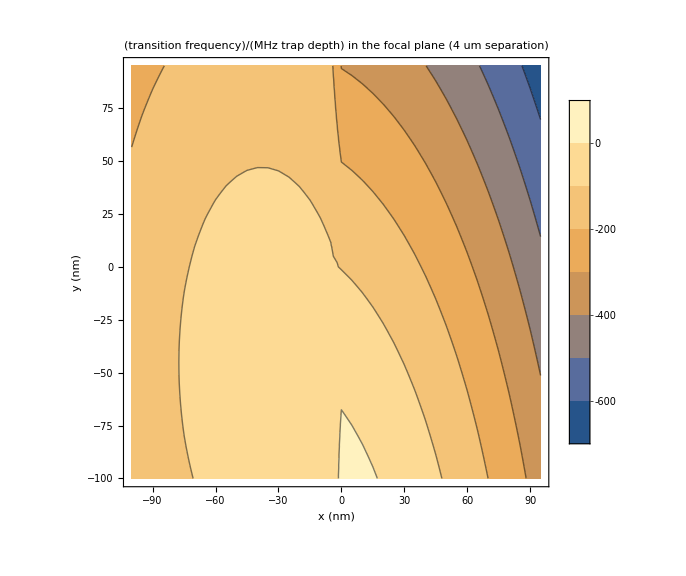

```mathematica
ListContourPlot[uFocalPlane,PlotLegends->Automatic,FrameLabel->{"x (nm)","y (nm)"},PlotLabel->"(transition frequency)/(MHz trap depth) in the focal plane\n(4 um separation)",LabelStyle->Directive[18],ImageSize->Large,PlotRange->All]
```

```mathematica
vals[[3]]/.{η->1/4 2π,θw->χ,Δ->1870-460,α00->(1870+2 460)/3}
```

35.2882

```mathematica
(π/2-ArcCos[1/(√3)])//N
```

0.61548

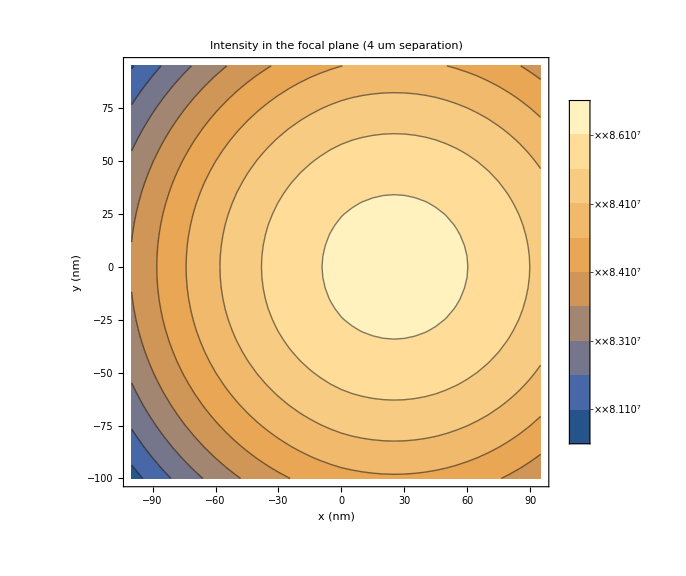

```mathematica
ListContourPlot[iFocalPlane,PlotLegends->Automatic,FrameLabel->{"x (nm)","y (nm)"},PlotLabel->"Intensity in the focal plane\n(4 um separation)",LabelStyle->Directive[18],ImageSize->Large,PlotRange->All]
```

```mathematica
findχ[evec_]:=Module[{evn,ell,d,tV,pMajor,pMinor},
evn=Normalize[evec];ell=ComplexExpand[Re[(evn)Exp[-ⅈ t]]];d=√(ell[[1]]^2+ell[[2]]^2+ell[[3]]^2);tV=NSolveValues[D[d,t]==0&&0<=t<2π&&d>√(1/2),t][[1]];
pMajor=ell/.t->tV;
pMinor=ell/.t->(tV+π/2);
χ=ArcTan[Norm[pMajor]/Norm[pMinor]]
]
```

```mathematica
χFocalPlane=ParallelTable[With[{x=eFocalPlane[[i,1]],y=eFocalPlane[[i,2]],e=eFocalPlane[[i,3]]},{x,y,45-Abs[180/π findχ[e]-45]}],{i,Length[eFocalPlane]}];
```

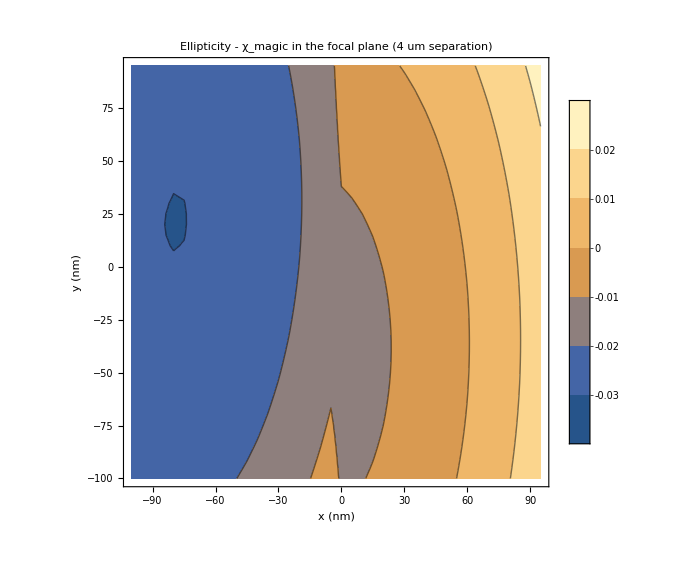

```mathematica
ListContourPlot[χFocalPlane,PlotLegends->Automatic,FrameLabel->{"x (nm)","y (nm)"},PlotLabel->"Ellipticity - χ_magic in the focal plane\n(4 um separation)",LabelStyle->Directive[18],ImageSize->Large,PlotRange->All]
```

```mathematica
SetDirectory["/Volumes/ni_lab/NaCs1pt5/NaCsSimulationPrecomputedMatrices/groundStateHamiltonian/"];
HacN=Import["HacN.mx"][[2;;4,2;;4]];
vals=FullSimplify[PowerExpand[FullSimplify[Eigenvalues[HacN]]]];
vals/.{η->1/4 2π,θw->π/2-ArcCos[1/(√3)]}//N
```

{(0.133333 Δ)/α00,-(0.133333 Δ)/α00,-(1.4803×10^-17 Δ)/α00}

```mathematica
pol[r_,ϕ_,z_]:=vals[[3]]/.{η->1/4 2π,θw->χ[r,ϕ,z],Δ->1870-460,α00->(1870+2 460)/3}
u[r_,ϕ_,z_]:=u0 intr[r,ϕ,z]pol[r,ϕ,z]
```

```mathematica
polFocalPlane=ParallelTable[With[{x=χFocalPlane[[i,1]],y=χFocalPlane[[i,2]],χ=χFocalPlane[[i,3]]},{x,y,vals[[3]]/.{η->1/4 2π,θw->χ,Δ->1870-460,α00->(1870+2 460)/3}}],{i,Length[eFocalPlane]}];
iMax=Max[iFocalPlane[[All,3]]];
uFocalPlane=ParallelTable[With[{x=polFocalPlane[[i,1]],y=polFocalPlane[[i,2]],i=iFocalPlane[[i,3]],p=polFocalPlane[[i,3]]},{x,y,10^6/iMax i p}],{i,Length[eFocalPlane]}];
```

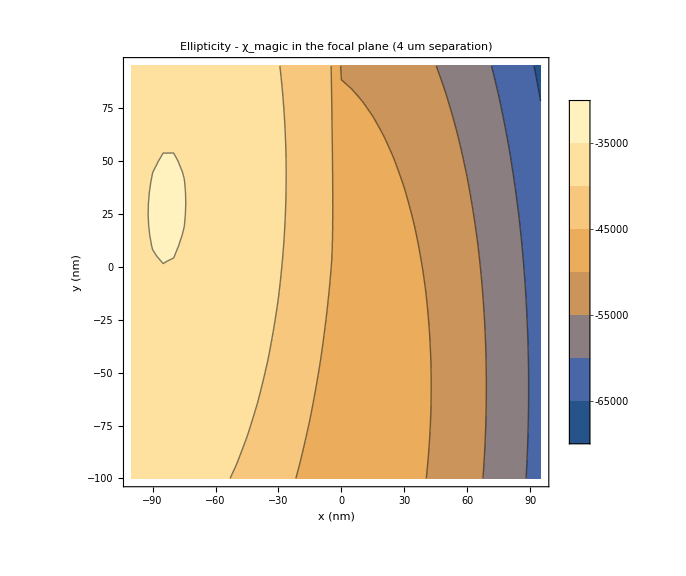

```mathematica
ListContourPlot[uFocalPlane,PlotLegends->Automatic,FrameLabel->{"x (nm)","y (nm)"},PlotLabel->"Ellipticity - χ_magic in the focal plane\n(4 um separation)",LabelStyle->Directive[18],ImageSize->Large,PlotRange->All]
```

```mathematica
p
```